# MOT calculations

```mathematica
constsdir="..\\constants\\";
imagedir=FileNameJoin[{NotebookDirectory[],"\\images\\"}];
AppendTo[$Path, FileNameJoin[{NotebookDirectory[],constsdir}]];
SetDirectory[NotebookDirectory[]];
<<"physconsts.m"
(*<<"rbconsts.m"*)
<<"csconsts.m"
conj[z_]:=z/.{ⅈ-> -ⅈ,-ⅈ->ⅈ};
SetOptions[Plot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 16],ImageSize->Medium];
SetOptions[PolarPlot,PolarAxes->True,PolarGridLines->Automatic,PolarTicks->{Drop[Table[i,{i,0,2 Pi,Pi/4}],-1],Automatic},LabelStyle->Directive[Black, 16],ImageSize->Medium];
SetOptions[ContourPlot,LabelStyle->Directive[Black, 16],ImageSize->Medium];

(*import from a file in future...*)
EHartreeSI = EHartree*e;
polarizabilityAU=(e^2 a0^2)/EHartreeSI;
c6AU=EHartreeSI a0^6;
```

## atom number

Number of atoms in a MOT can be estimated using the known photon collection efficiency (EMCCD’s quantum efficiency * collection lens fractional solid angle), the number of measured photons within some interval, and the scattering rate per photon. 

In the lab, the rate of atoms loaded into a MOT is given by R = R_ph/(R_scat Δt η) where R_ph is the rate of photons incident on the camera, R_scat is the calculated single atom scattering rate, Δt is the exposure time, and η is the collection efficiency of the system.

```mathematica
(*Rb87 params*)
(*Γ=ΓD2; (*s^-1*)
Ι=6*2*.250/(π 0.01^2); (*mW/cm^2 for 6 Gaussian MOT beams*)
Ω=Γ √(Ι/IsatD2);
Δ =1.5*Γ;*)
(*Cs133 params*)
Γ=ΓD2; (*s^-1*)
Ι=6*2*.250/(π 0.01^2); (*mW/cm^2 for 6 Gaussian MOT beams*)
Ω=Γ √(Ι/IsatD2);
Δ =1.5*Γ;
Rscat =(Γ Ω^2)/(2 Ω^2+4 Δ^2+Γ^2);
"Scattering rate [Hz] per atom"
Rscat/(2π)
(*collection efficiency params*)
lensNA =0.55;
lensθ=ArcSin[lensNA];
quantumEfficiency=0.6;(*EMCCD efficiency*)
"System collection efficiency"
fractionalSolidAngle = Integrate[Sin[θ],{θ,0,lensθ},{ϕ,0,2π}]/(4π);
totalEfficiency = quantumEfficiency *fractionalSolidAngle
```

Scattering rate [Hz] per atom

2.60909×10^6

System collection efficiency

0.0494506

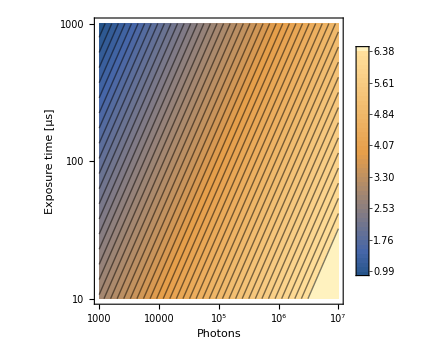

```mathematica
ContourPlot[Log10[photons/(totalEfficiency*Rscat/(2π)*time*10^-6)],{photons,10^3,10^7},{time,10,10^3},Contours-> 50,PlotLegends->Automatic,ScalingFunctions->{"Log","Log"},FrameLabel->{"Photons","Exposure time [μs]"}]
```

## vacuum pressure measurement

```mathematica
(*van der Waals coefficient "C6" between atoms of the same species with n valence electrons*)
PaPerTorr = 133.322;
αdcRb = 4π ϵ0 *47.398*10^-30;
αdcCs = 4π ϵ0 *59.399*10^-30;
CvdW[αDC_,nvalence_]:=3/4(ℏ e)/((4π ϵ0)^2 me^(1/2))αDC^(3/2)nvalence^(1/2);
(*loss coefficients [decay rate per pressure] between cooled and uncooled atoms of the same species. T is background temp [K], m is atom mass, D is trap depth [K]*)
γperP[Tatom_,CvdW_,m_,Ttrap_]:= 6.8*1/(kB Tatom)^(2/3)(CvdW/m)^(1/3)(kB Ttrap m)^(-1/6);
```

```mathematica
1/0.00750062
```

133.322

```mathematica
kB
```

1.3807×10^-23

```mathematica
CvdW[αdcRb,1]/c6AU (*matches Sackett paper to within a few percent*)
CvdW[αdcCs,1]/c6AU
```

4283.04

6008.7

```mathematica
γperP[300,CvdW[αdcRb,1],mRb,1]PaPerTorr
```

4.46971×10^7

Compute γperP for Cs and produce function from rrcat.gov for MOT lifetime vs pressure